```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\87F21"];
data=Import[#]&/@FileNames["*csv"];
data2=Table[Take[data[[i]],{17,-2}],{i,1,Length[data]}];
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\87F21\\Off"];
dataoff=Import[#]&/@FileNames["*csv"];
data2off=Table[Take[dataoff[[i]],{17,-2}],{i,1,Length[dataoff]}];
```

```mathematica
f[data_]:=Module[{ll,max,min,yaxis1,yaxis2,wcn,ff,gg,loc,kk},
ll=data[[All,2]];
{max,min}=#[ll]&/@{Max,Min};
yaxis1=Take[data[[All,4]],Flatten[{#[ll,max][[1]],#[ll,min][[-1]]}&@Position]];
yaxis2=Take[data[[All,8]],Flatten[{#[ll,max][[1]],#[ll,min][[-1]]}&@Position]];

wcn=(794.76728224*10^-9);


ff[x_]:=Evaluate[Fit[


Flatten[{Table[{o,yaxis1[[o]]},{o,10,200}],Table[{o,yaxis1[[o]]},{o,Length[yaxis1]-200,Length[yaxis1]-10}]},1]

,{1,x},x]];
gg=Table[ff[x],{x,1,Length[yaxis1]}];
loc=Select[FindPeaks[
GaussianFilter[yaxis2,30]
,15,0.000001],1500<#[[1]]<5500&];
kk[x_]:=Evaluate[Fit[{{loc[[1,1]],-0.816},{loc[[-1,1]],0}},{1,x},x]];
{-12.531885282826405 wcn Log[yaxis1/gg],GaussianFilter[yaxis1/gg,10],yaxis2,Table[kk[x],{x,1,Length[yaxis1]}]}

]
```

```mathematica
Manipulate[
ListPlot[{GaussianFilter[data2[[i]][[All,8]],30],
Select[FindPeaks[
GaussianFilter[data2[[i]][[All,8]],30]
,15,0.000001],1500<#[[1]]<5500&]},PlotStyle->{Black,{Red,AbsolutePointSize[5]}}]
,{{i,22},1,Length[data2],1}]
```

```mathematica
Manipulate[ListPlot[Transpose[f[data2[[i]]][[{4,2}]]],PlotRange->{{-0.02,0.04},{0.4,0.55}},Joined->True,Epilog->Line[{{-2,1},{2,1}}]],{{i,2},1,Length[data2],1}]
```

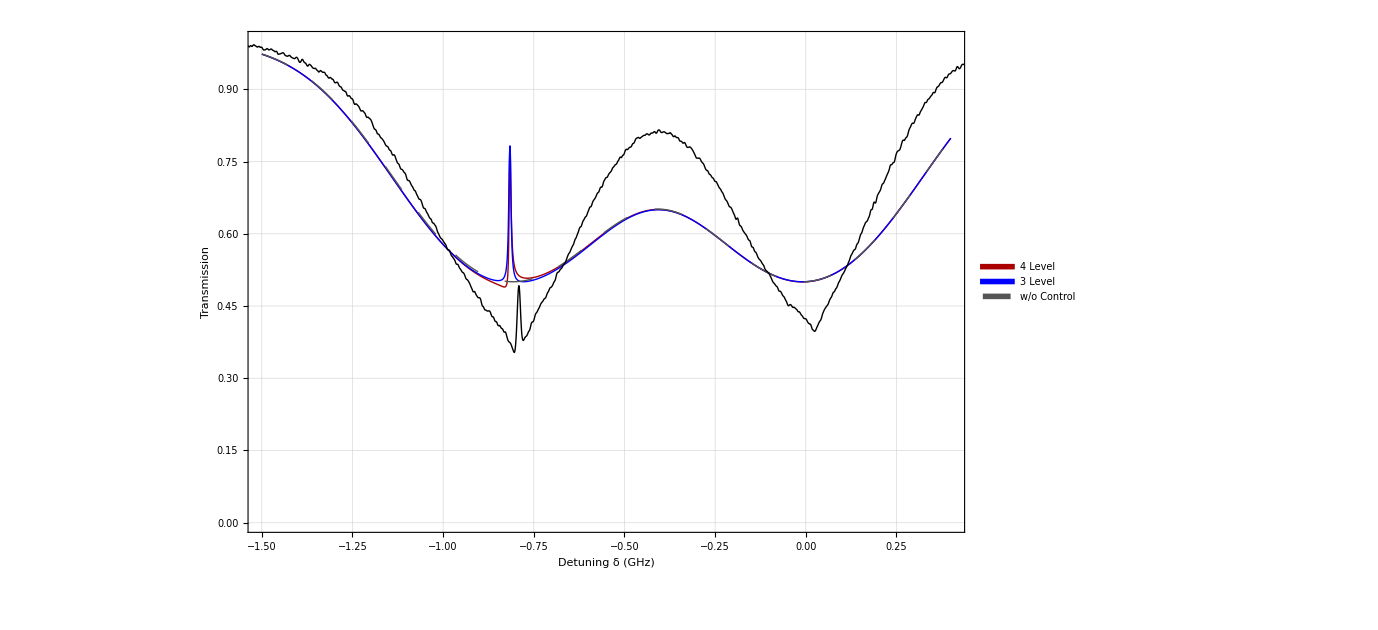

```mathematica
final2=ListPlot[{Lev4DoppTestsc[32,15/1000,0.9/1000,1.438*10^6,-816*10^6,0],Lev3DoppTestsc[32,15/1000,0.9/1000,1.438*10^6,-816*10^6,0],Lev3DoppTestsc[32,0/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Bottom}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[1],Darker[Red]},{AbsoluteThickness[1],Blue},{AbsoluteThickness[1],Darker[Gray],Dashing[.02]},{AbsoluteThickness[1],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-1.5,0.4},{0.0,1.0}}];
Show[final2,ListPlot[Transpose[f[data2[[46]]][[{4,2}]]],Joined->True,PlotStyle->{Thick,Black},Epilog->Line[{{-2,1},{2,1}}]]]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-1.5,0.4,0.0003]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[1/18]*2.5373 10^-29;
d41=Sqrt[5/18]*2.5373 10^-29;
d32=Sqrt[1/6]*2.5373 10^-29;
d42=Sqrt[1/6]*2.5373 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(816*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254*3/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-1.5,0.4,0.0003]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[1/18]*2.5373 10^-29;
d41=Sqrt[5/18]*2.5373 10^-29;
d32=Sqrt[1/6]*2.5373 10^-29;
d42=Sqrt[1/6]*2.5373 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(816*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254*3/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]

,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]
}],
Transpose[{d/10^9,
Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]]
]
```

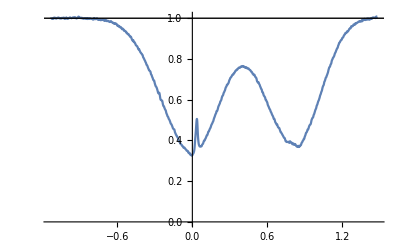

```mathematica
ListPlot[Transpose[f[data2[[-1]]][[{4,2}]]],Joined->True,Epilog->Line[{{-2,1},{2,1}}]]
```

```mathematica
EITmax8721
```

{0.478798,0.479331,0.474435,0.47502,0.462905,0.462799,0.462175,0.468082,0.464645,0.461179,0.463418,0.46429,0.460151,0.462973,0.462826,0.457547,0.467096,0.469872,0.465322,0.467322,0.468968,0.468366,0.46911,0.471026,0.466275,0.468879,0.472102,0.466558,0.465006,0.47053,0.470286,0.465521,0.464058,0.470668,0.469901,0.473264,0.488176,0.475928,0.478012,0.476808,0.482089,0.481541,0.483201,0.482278,0.456288,0.492297,0.485312,0.489478,0.49934,0.494026,0.495244,0.498052,0.498858,0.49704,0.504781,0.485936,0.50189,0.502768,0.503803,0.503796,0.509364,0.505164,0.508587,0.510215,0.509763,0.50551,0.508696,0.501541,0.507914,0.509045,0.51141,0.512283,0.514636,0.505017,0.50903,0.512586,0.504862,0.510861,0.487662,0.504804,0.505549,0.50668,0.505477,0.505597}

```mathematica
pw={0.5,1,2,3,4,5,6,7,8,9,10,15,20,25,30,35,40,50,60,70,80};power=Flatten[Transpose[{pw,pw,pw,pw}]];
EITmax8721=Table[
If[i<5,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.02-0.816<#[[1]]<0.00-0.816&][[All,2]]//Max,
If[i<27,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01-0.816<#[[1]]<0.015-0.816&][[All,2]]//Max,
Select[Transpose[f[data2[[i]]][[{4,2}]]],0.005-0.816<#[[1]]<0.04-0.816&][[All,2]]//Max
]
],{i,1,Length[data],1}];
```

```mathematica
pw={0.5,1,2,3,4,5,6,7,8,9,10,15,20,25,30,35,40,50,60,70,80};power=Flatten[Transpose[{pw,pw,pw,pw}]];
EITmin8721=Table[
If[i<5,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.02-0.816<#[[1]]<0.00-0.816&][[All,2]]//Min,
If[i<27,
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.01-0.816<#[[1]]<0.015-0.816&][[All,2]]//Min,
Select[Transpose[f[data2[[i]]][[{4,2}]]],0.005-0.816<#[[1]]<0.04-0.816&][[All,2]]//Min
]
],{i,1,Length[data],1}];
```

```mathematica
EITmax8721
```

{0.478798,0.479331,0.474435,0.47502,0.462905,0.462799,0.462175,0.468082,0.464645,0.461179,0.463418,0.46429,0.460151,0.462973,0.462826,0.457547,0.467096,0.469872,0.465322,0.467322,0.468968,0.468366,0.46911,0.471026,0.466275,0.468879,0.472102,0.466558,0.465006,0.47053,0.470286,0.465521,0.464058,0.470668,0.469901,0.473264,0.488176,0.475928,0.478012,0.476808,0.482089,0.481541,0.483201,0.482278,0.456288,0.492297,0.485312,0.489478,0.49934,0.494026,0.495244,0.498052,0.498858,0.49704,0.504781,0.485936,0.50189,0.502768,0.503803,0.503796,0.509364,0.505164,0.508587,0.510215,0.509763,0.50551,0.508696,0.501541,0.507914,0.509045,0.51141,0.512283,0.514636,0.505017,0.50903,0.512586,0.504862,0.510861,0.487662,0.504804,0.505549,0.50668,0.505477,0.505597}

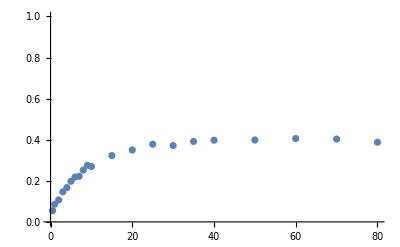

```mathematica
rb8721=ListPlot[{Transpose[{pw,1-Log[Max/@Partition[EITmax8721,4]]/Log[Min/@Partition[EITmin8721,4]]}]},PlotRange->{0,1}]
```

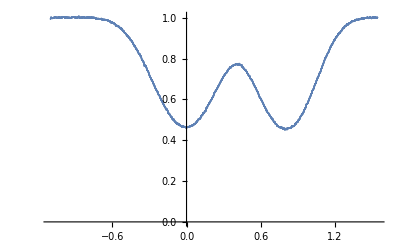

```mathematica
ListPlot[Transpose[f[data2off[[3]]][[{4,2}]]]]
```

```mathematica
((Select[Transpose[f[data2off[[1]]][[{4,2}]]],-0.02<#[[1]]<0.04&][[All,2]]//Min)
+(Select[Transpose[f[data2off[[2]]][[{4,2}]]],-0.02<#[[1]]<+0.04&][[All,2]]//Min)
+(Select[Transpose[f[data2off[[3]]][[{4,2}]]],-0.02<#[[1]]<+0.04&][[All,2]]//Min))/3
```

0.459205

```mathematica
Table[Select[Transpose[f[data2off[[i]]][[{4,2}]]],-0.02<#[[1]]<0.04&][[All,2]]//Min,{i,1,Length[dataoff],1}]//Mean
```

0.819396

```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\87F22\\Off"];
dataoff=Import[#]&/@FileNames["*csv"];
data2off=Table[Take[dataoff[[i]],{17,-2}],{i,1,Length[dataoff]}];
```